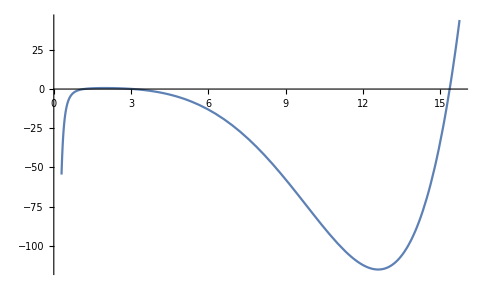

```mathematica
Clear[k,m,ss,om,jj];
(*m1r=k r^3;
m2r=m;
msr= 4 Pi ss r^2;*)
k=0;
m=1;
om=0.1;  (* ω *)
jj=0.5;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/(1-2k m^2 x^2)^2;
q0=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2;
q4=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f1=Plot[q0,{x,0.3, 15.75},PlotRange->All]
```

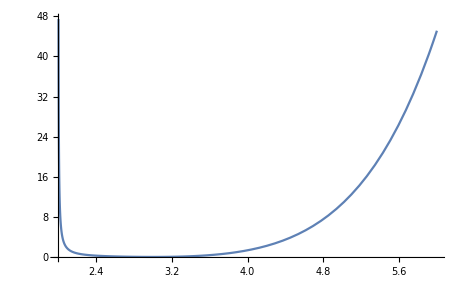

```mathematica
f1a=Plot[q2,{x,2.004, 6},PlotRange->All]
```

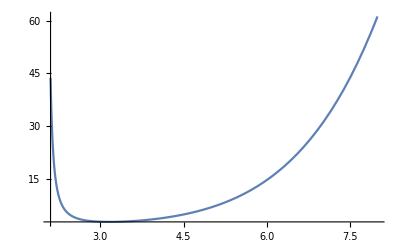

```mathematica
f1b=Plot[q4,{x,2.1, 8},PlotRange->All]
```

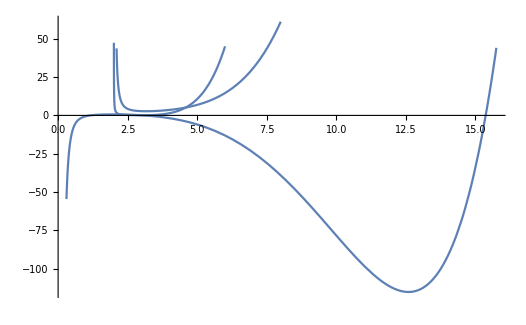

```mathematica
Show[f1,f1a,f1b]
```

```mathematica
q01=FullSimplify[q0]
```

0.961844-1.5/x^3+0.0161862 x^3-0.0157914 x^4+0.0000623418 x^6

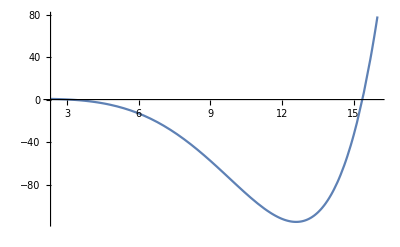

```mathematica
Plot[q01,{x,2.3,16}]
```

```mathematica
q01p=D[q01,x]
```

4.5/x^4+0.0485585 x^2-0.0631655 x^3+0.000374051 x^5

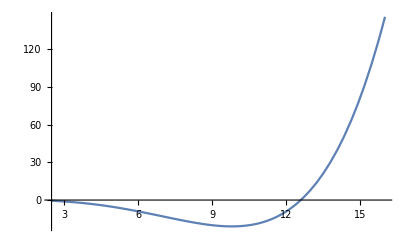

```mathematica
Plot[q01p,{x,2.5,16},PlotRange->All]
```

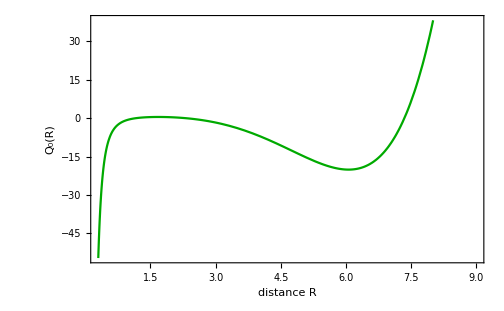

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; msr= 4 Pi ss r^2;*)
k=0;
m=1;
om=0.2;  (* ω *)
jj=0.5;
Omega=2 jj/x^3;  (* Ω *)
ss=0.02;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0a=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2a=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2;
q4a=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f2=Plot[q0a,{x,0.3,9},Frame->True,FrameLabel->{"distance R"," Q_0(R)"},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

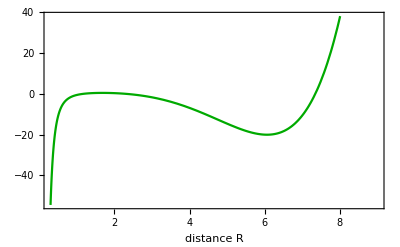

```mathematica
f20=Plot[q0a,{x,0.3,9},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

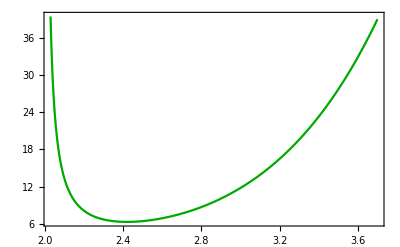

```mathematica
f2a=Plot[q2a,{x,2.03,3.7},Frame->True,PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

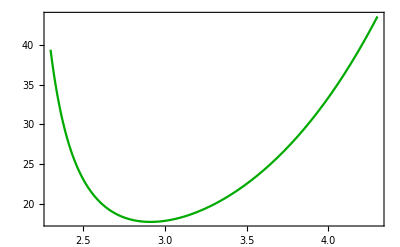

```mathematica
f2b=Plot[q4a,{x,2.3,4.3},Frame->True,PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->False]
```

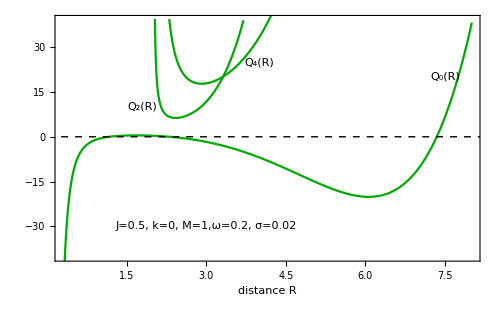

```mathematica
fig1a=Show[f20,f2a,f2b, Graphics[{Inset[Framed["J=0.5, k=0, M=1,ω=0.2, σ=0.02"],{3,-30},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{1.8,10},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{7.5,20},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{4,25},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-40,39}]
```

```mathematica
Export["D:fig1a.pdf",fig1a,"PDF"];
Export["D:fig1a.eps", fig1a];
```

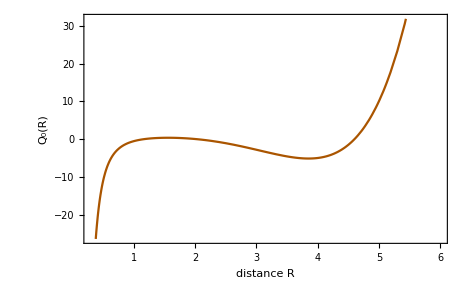

```mathematica
Clear[k,m,ss,om,jj];(*m1r=k r^3; m2r=m; mmsr= 4 Pi ss r^2;*)
k=0;
m=1;
om=0.3;  (* ω *)
jj=0.5;
Omega=2 jj/x^3;  (* Ω *)
ss=0.03;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0b=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
q2b=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2;
q4b=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
f3=Plot[q0b,{x,0.3,6},Frame->True,FrameLabel->{"distance R","Q_0(R)"},PlotStyle->{Darker[Orange]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",16,GrayLevel[0],Bold}]
```

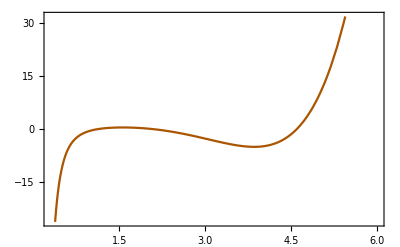

```mathematica
f3aa=Plot[q0b,{x,0.3,6},Frame->True,FrameLabel->{"",""},PlotStyle->{Darker[Orange]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

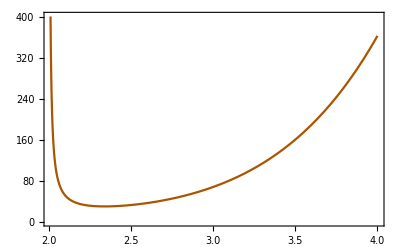

```mathematica
f3a=Plot[q2b,{x,2.01,4},Frame->True,PlotStyle->{Darker[Orange]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

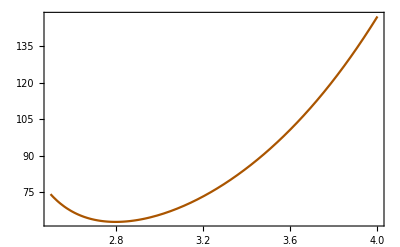

```mathematica
f3b=Plot[q4b,{x,2.5,4},Frame->True,PlotStyle->{Darker[Orange]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

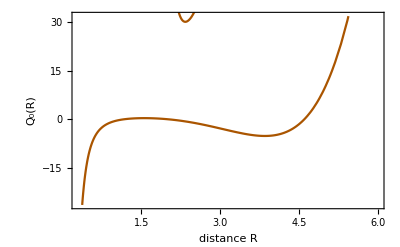

```mathematica
Show[f3,f3a,f3b]
```

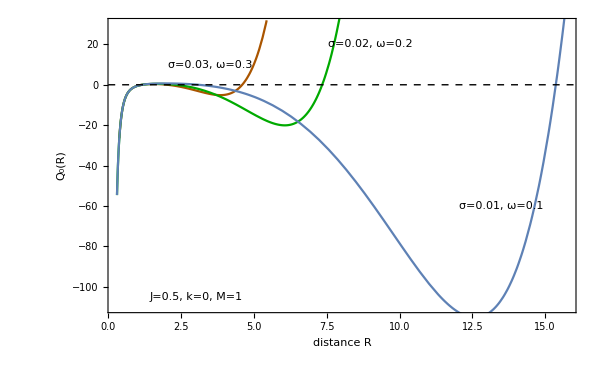

```mathematica
fd01=Show[f3,f2,f1,Graphics[{Inset[Framed["J=0.5, k=0, M=1"],{3,-105},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",16}]}],Graphics[{Inset["σ=0.01, ω=0.1",{13.5,-60},BaseStyle->{Italic,Bold,Purple,FontFamily->"Times",14}]}],Graphics[{Inset["σ=0.02, ω=0.2",{9,20},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",14}]}],Graphics[{Inset["σ=0.03, ω=0.3",{3.5,10},BaseStyle->{Italic,Bold,Darker[Red],FontFamily->"Times",14}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},ImageSize->600,PlotRange->{-110,30},Axes->False]
```

```mathematica
Export["D:fd01.pdf",fd01,"PDF"];
```

```mathematica
Export["D:fd01.eps", fd01];
```

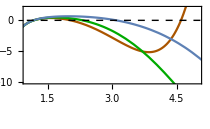

```mathematica
fd01small=Show[f3aa,f2,f1,Graphics[{Inset[Framed["J=0.5, k=0, M=1"],{2.5,-80},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",22},ImageSize->210,PlotRange->{{1,5},{-10,2}},Axes->False]
```

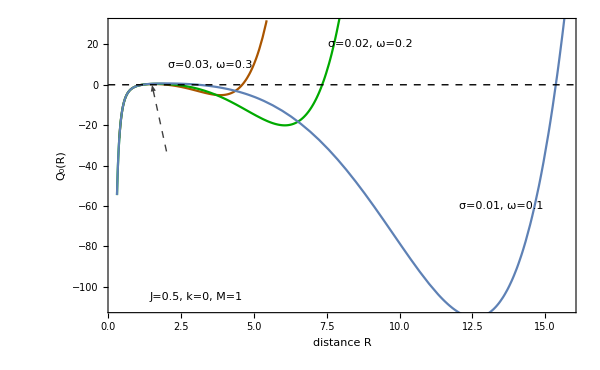

```mathematica
fig1=Show[fd01,Epilog->{Inset[fd01small,Scaled[{0.25,0.35}]],Dashed,Darker[Gray,0.5],Arrowheads[Medium],Arrow[{{2,-33},{1.5,0}}],{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,FontFamily->"Times",20},LabelStyle->Directive[Black,Large,Bold]]
```

```mathematica
Export["D:fig1.pdf",fig1,"PDF"];
Export["D:fig1.eps", fig1];
```

```mathematica
(************************************************************************************************************************************)
Clear[k,m,ss,om,jj];
(*m1r=k r^3;
m2r=m;
msr= 4 Pi ss r^2;*)
k=0;
m=1;
om=0.1;  (* ω *)
(*jj=38.559;*)
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
dq0=D[q0,x]
ddq0=D[dq0,x]
q2=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2;
q4=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
Solve[{q0==0,dq0==0},{x,jj}]
```

-0.0631655 x^3-0.0118435 (-(12 jj^2)/x^6-(0.2 jj)/x^3) x^5+3/2 (-(12 jj^2)/x^6-(0.2 jj)/x^3) x^2 (1-0.00789568 x^3)+1/2 ((72 jj^2)/x^7+(0.6 jj)/x^4) x^3 (1-0.00789568 x^3)+0.0473741 x^2 (1+0.00789568 x^3)

-0.189496 x^2+0.00112215 x^4-0.0947482 (-(12 jj^2)/x^6-(0.2 jj)/x^3) x^4-0.0236871 ((72 jj^2)/x^7+(0.6 jj)/x^4) x^5+3 (-(12 jj^2)/x^6-(0.2 jj)/x^3) x (1-0.00789568 x^3)+3 ((72 jj^2)/x^7+(0.6 jj)/x^4) x^2 (1-0.00789568 x^3)+1/2 (-(504 jj^2)/x^8-(2.4 jj)/x^5) x^3 (1-0.00789568 x^3)+0.0947482 x (1+0.00789568 x^3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-14.7669,jj→88.9168},{x→-12.5751,jj→-45.2521},{x→-3.07481-5.19078 ⅈ,jj→-15.5927+32.8944 ⅈ},{x→-3.07481+5.19078 ⅈ,jj→-15.5927-32.8944 ⅈ},{x→-2.993-5.29541 ⅈ,jj→11.8826-32.8785 ⅈ},{x→-2.993+5.29541 ⅈ,jj→11.8826+32.8785 ⅈ},{x→-2.079-0.0560547 ⅈ,jj→0.0747136-0.885167 ⅈ},{x→-2.079+0.0560547 ⅈ,jj→0.0747136+0.885167 ⅈ},{x→0.186414-2.19073 ⅈ,jj→0.58658+0.766588 ⅈ},{x→0.186414+2.19073 ⅈ,jj→0.58658-0.766588 ⅈ},{x→0.279053-2.26928 ⅈ,jj→-0.528465-0.945103 ⅈ},{x→0.279053+2.26928 ⅈ,jj→-0.528465+0.945103 ⅈ},{x→2.54969,jj→1.26286},{x→2.68035,jj→-1.56195},{x→5.9407,jj→-27.7424},{x→6.13154,jj→24.0934},{x→11.5899,jj→38.5593},{x→13.8125,jj→-73.7584}}

```mathematica
q2/.{x->11.589886436601981,jj->38.55926844750041}
q4/.{x->11.589886436601981,jj->38.55926844750041}
ddq0/.{x->11.589886436601981,jj->38.55926844750041}
```

5147.18

434.1

10.9948

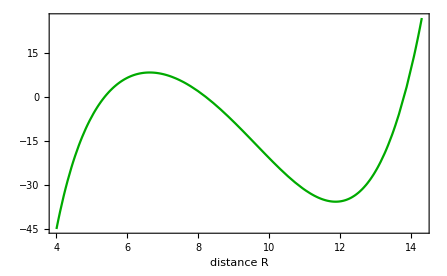

```mathematica
ftest1=Plot[q0/.{jj->30},{x,4, 14.3},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

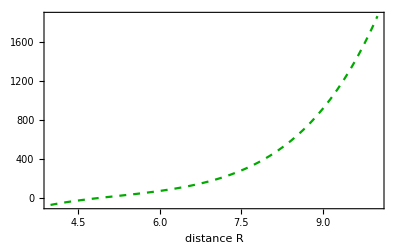

```mathematica
ftest1a=Plot[q2/.{jj->30},{x,4, 10},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R"," "},PlotStyle->{Dashed,Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

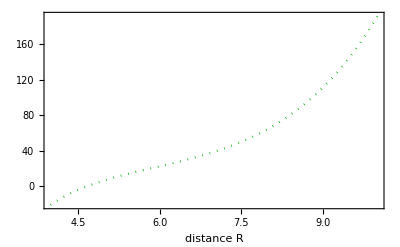

```mathematica
ftest1b=Plot[q4/.{jj->30},{x,4, 10},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dotted,Darker[Green]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

```mathematica
Clear[k,m,ss,om,jj];
(*m1r=k r^3;
m2r=m;
msr= 4 Pi ss r^2;*)
k=0;
m=1;
om=0;  (* ω *)
jj=30;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0om=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2om=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4om=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0om=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0om-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
dq0om=D[q0,x]
ddq0om=D[dq0,x]
q2om=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2om;
q4om=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4om +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
```

-0.0631655 x^3-0.0118435 (-10800/x^6-6./x^3) x^5+3/2 (-10800/x^6-6./x^3) x^2 (1-0.00789568 x^3)+1/2 (64800/x^7+18./x^4) x^3 (1-0.00789568 x^3)+0.0473741 x^2 (1+0.00789568 x^3)

-0.189496 x^2+0.00112215 x^4-0.0947482 (-10800/x^6-6./x^3) x^4-0.0236871 (64800/x^7+18./x^4) x^5+3 (-10800/x^6-6./x^3) x (1-0.00789568 x^3)+3 (64800/x^7+18./x^4) x^2 (1-0.00789568 x^3)+1/2 (-453600/x^8-72./x^5) x^3 (1-0.00789568 x^3)+0.0947482 x (1+0.00789568 x^3)

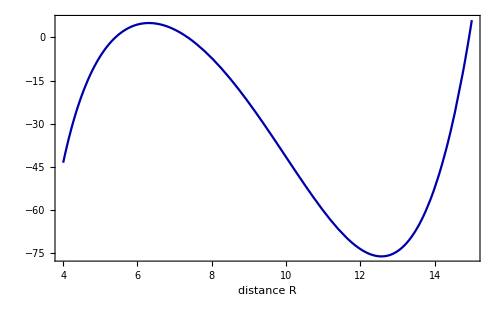

```mathematica
ftest1om=Plot[q0om/.{jj->30,om->0},{x,4, 15},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

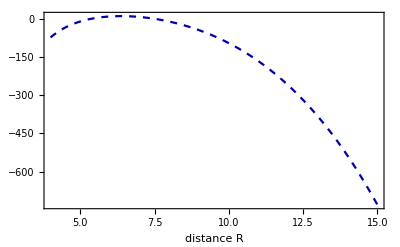

```mathematica
ftest1oma=Plot[q2om/.{jj->30,om->0},{x,4, 15},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dashed,Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

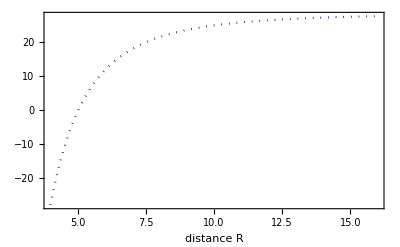

```mathematica
ftest1omb=Plot[q4om/.{jj->30,om->0},{x,4, 16},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dotted,Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

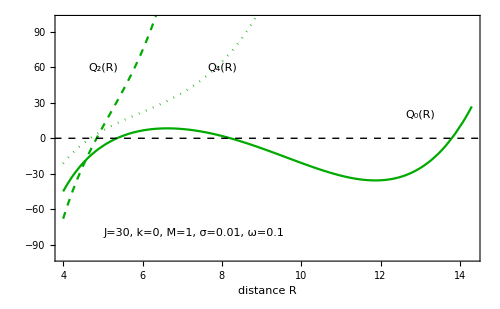

```mathematica
f1=Show[ftest1,ftest1a,ftest1b,Graphics[{Inset[Framed["J=30, k=0, M=1, σ=0.01, ω=0.1"],{7.3,-80},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{5,60},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{8,60},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{13,20},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}], FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-100,100}]
```

```mathematica
Export["C:\\Users\\Giannis\\OneDrive - ΠΑΝΕΠΙΣΤΗΜΙΟ ΙΩΑΝΝΙΝΩΝ\\Έγγραφα\\fig1.eps",f1,"EPS"]
```

C:\Users\Giannis\OneDrive - ΠΑΝΕΠΙΣΤΗΜΙΟ ΙΩΑΝΝΙΝΩΝ\Έγγραφα\fig1.eps

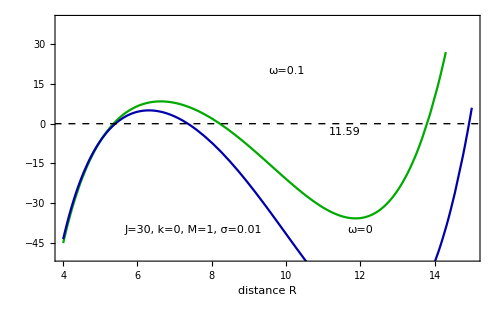

```mathematica
fgt=Show[ftest1,ftest1om, Graphics[{Inset[Framed["J=30, k=0, M=1, σ=0.01"],{7.5,-40},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["11.59",{11.59,-3},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset["ω=0.1",{10,20},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["ω=0",{12,-40},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}], FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-50,39}]
```

```mathematica
Export["D:fgt.pdf",fgt,"PDF"];
```

```mathematica
Clear[k,m,ss,om,jj];
(*m1r=k r^3;
m2r=m;
msr= 4 Pi ss r^2;*)
(*k=0.11876;*)
m=1;
om=0.1;  (* ω *)
jj=0.1;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
dq0=D[q0,x]
ddq0=D[dq0,x]
q2=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2;
q4=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4 +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
Solve[{q0==0,dq0==0},{x,k}]
```

-12 (k+0.00394784 x) x^2-0.0157914 x^3+1/2 (-0.12/x^6-0.02/x^3) x^3 (-0.0236871 x^2-3 k x^2)+3/2 (-0.12/x^6-0.02/x^3) x^2 (1-0.00789568 x^3-k x^3)+1/2 (0.72/x^7+0.06/x^4) x^3 (1-0.00789568 x^3-k x^3)+2 (0.0236871 x^2+3 k x^2) (1+0.00789568 x^3+k x^3)

-24 (k+0.00394784 x) x-0.0947482 x^2+1/2 (-0.12/x^6-0.02/x^3) x^3 (-0.0473741 x-6 k x)+3 (-0.12/x^6-0.02/x^3) x^2 (-0.0236871 x^2-3 k x^2)+(0.72/x^7+0.06/x^4) x^3 (-0.0236871 x^2-3 k x^2)+2 (0.0236871 x^2+3 k x^2)^2+3 (-0.12/x^6-0.02/x^3) x (1-0.00789568 x^3-k x^3)+3 (0.72/x^7+0.06/x^4) x^2 (1-0.00789568 x^3-k x^3)+1/2 (-5.04/x^8-0.24/x^5) x^3 (1-0.00789568 x^3-k x^3)+2 (0.0473741 x+6 k x) (1+0.00789568 x^3+k x^3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-3.23478×10^16,k→0.},{x→-4.09104,k→0.0150466},{x→-0.614325-0.212927 ⅈ,k→-1.85051+3.39472 ⅈ},{x→-0.614325+0.212927 ⅈ,k→-1.85051-3.39472 ⅈ},{x→-0.347864-0.564891 ⅈ,k→2.96834+0.207931 ⅈ},{x→-0.347864+0.564891 ⅈ,k→2.96834-0.207931 ⅈ},{x→-0.247873-0.430174 ⅈ,k→4.14765+0.0140687 ⅈ},{x→-0.247873+0.430174 ⅈ,k→4.14765-0.0140687 ⅈ},{x→0.0973935-0.663384 ⅈ,k→-1.2373-3.25222 ⅈ},{x→0.0973935+0.663384 ⅈ,k→-1.2373+3.25222 ⅈ},{x→0.495779,k→4.12358},{x→0.507536-0.463304 ⅈ,k→-1.81292+2.70181 ⅈ},{x→0.507536+0.463304 ⅈ,k→-1.81292-2.70181 ⅈ},{x→0.715123,k→2.45456},{x→0.955479-4.6172 ⅈ,k→-0.00252544+0.016642 ⅈ},{x→0.955479+4.6172 ⅈ,k→-0.00252544-0.016642 ⅈ},{x→2.01363,k→0.118764},{x→6.16581,k→-0.0204038},{x→3.23478×10^16,k→0.}}

```mathematica
q2/.{x->2.01363282883879,k->0.11876385886883054}
q4/.{x->2.01363282883879,k->0.11876385886883054}
ddq0/.{x->2.01363282883879,k->0.11876385886883054}
q0/.{x->2.01363282883879,k->0.11876385886883054}
```

2.54651

170.522

4.45881

-8.88178×10^-16

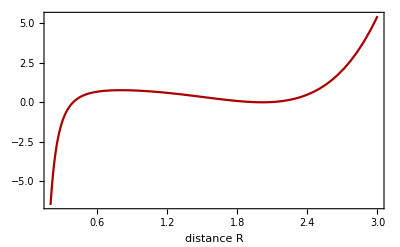

```mathematica
ftest2=Plot[q0/.{k->0.11876385886883054},{x,0.2, 3},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Red]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

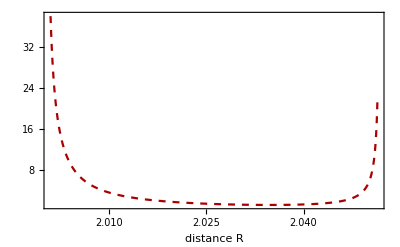

```mathematica
ftest2a=Plot[q2/.{k->0.11876385886883054},{x,2.001, 2.0514},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dashed,Darker[Red]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

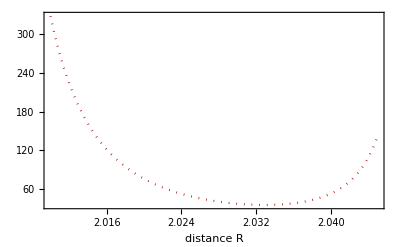

```mathematica
ftest2b=Plot[q4/.{k->0.11876385886883054},{x,2.01, 2.045},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dotted,Darker[Red]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

```mathematica
Clear[k,m,ss,om,jj];
(*m1r=k r^3;
m2r=m;
msr= 4 Pi ss r^2;*)
(*k=0.11876;*)
m=1;
om=0;  (* ω *)
jj=0.1;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0omn=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2omn=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4omn=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0omn=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0omn-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
dq0omn=D[q0omn,x]
ddq0omn=D[dq0omn,x]
q2omn=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2omn;
q4omn=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4omn +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
```

-12 (k+0.00394784 x) x^2-0.0157914 x^3+1/2 (0.-0.12/x^6) x^3 (-0.0236871 x^2-3 k x^2)+(0.36 (1-0.00789568 x^3-k x^3))/x^4+3/2 (0.-0.12/x^6) x^2 (1-0.00789568 x^3-k x^3)+2 (0.0236871 x^2+3 k x^2) (1+0.00789568 x^3+k x^3)

-24 (k+0.00394784 x) x-0.0947482 x^2+1/2 (0.-0.12/x^6) x^3 (-0.0473741 x-6 k x)+(0.72 (-0.0236871 x^2-3 k x^2))/x^4+3 (0.-0.12/x^6) x^2 (-0.0236871 x^2-3 k x^2)+2 (0.0236871 x^2+3 k x^2)^2-(0.36 (1-0.00789568 x^3-k x^3))/x^5+3 (0.-0.12/x^6) x (1-0.00789568 x^3-k x^3)+2 (0.0473741 x+6 k x) (1+0.00789568 x^3+k x^3)

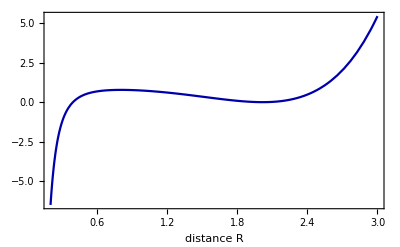

```mathematica
ftest2om=Plot[q0omn/.{k->0.11876385886883054},{x,0.2, 3},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

```mathematica
q2omn/.{x->2.01363282883879,k->0.11876385886883054}
q4omn/.{x->2.01363282883879,k->0.11876385886883054}
ddq0omn/.{x->2.01363282883879,k->0.11876385886883054}
q0omn/.{x->2.01363282883879,k->0.11876385886883054}
```

-0.248288

0.122884

4.44351

-0.000341386

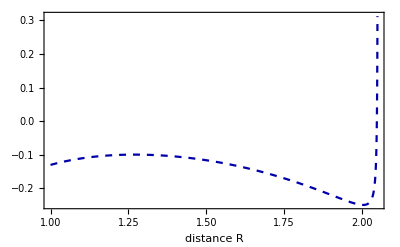

```mathematica
ftest2oma=Plot[q2omn/.{k->0.11876385886883054},{x,1, 2.05},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dashed,Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

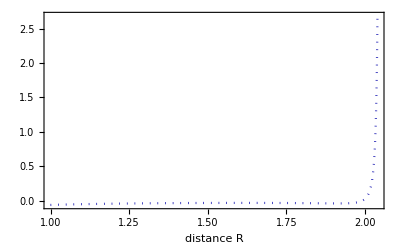

```mathematica
ftest2omb=Plot[q4omn/.{k->0.11876385886883054},{x,1, 2.04},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dotted,Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold}]
```

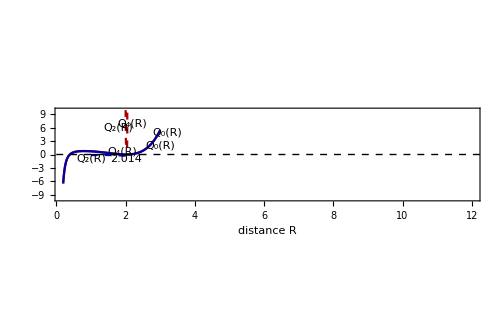

```mathematica
f2=Show[ftest2,ftest2a,ftest2b,ftest2om,ftest2oma, Graphics[{Inset[Framed["J=38.56, k=0, M=1, σ=0.01"],{7.3,-80},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["2.014",{2.014,-1},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{1.8,6},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{2.2,7},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{3.2,5},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{3,2},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{1,-1},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)",{1.9,0.7},BaseStyle->{Italic,Bold,Blue,FontFamily->"Times",12}]}],Graphics[{Inset["ω=0.1",{10,20},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["ω=0",{12,-40},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}], FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-10,10},Axes->{True,False}]
```

```mathematica
Export["D:f2.pdf",f2,"PDF"];
```

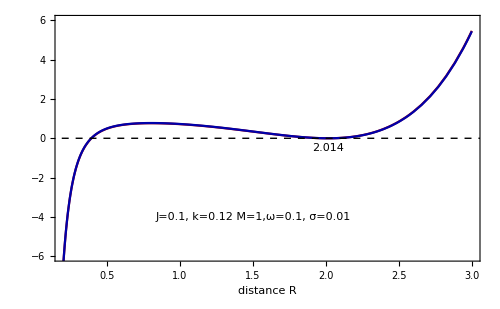

```mathematica
fgt1=Show[ftest2,ftest2om, Graphics[{Inset[Framed["J=0.1, k=0.12 M=1,ω=0.1, σ=0.01"],{1.5,-4},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["2.014",{2.014,-0.5},BaseStyle->{Italic,Bold,Red,FontFamily->"Times",12}]}],FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-6,6}]
```

```mathematica
Export["D:fgt1.pdf",fgt1,"PDF"];
```

```mathematica
q0
q0omn
p0
p0omn
```

-4 (k+0.00394784 x) x^3+1/2 (-0.12/x^6-0.02/x^3) x^3 (1-0.00789568 x^3-k x^3)+(1+0.00789568 x^3+k x^3)^2

-4 (k+0.00394784 x) x^3+1/2 (0.-0.12/x^6) x^3 (1-0.00789568 x^3-k x^3)+(1+0.00789568 x^3+k x^3)^2

1/2 (-0.12/x^6-0.02/x^3)

1/2 (0.-0.12/x^6)

```mathematica
Clear[k,m,ss,om,jj];
(*m1r=k r^3;
m2r=m;
msr= 4 Pi ss r^2;*)
(*k=0.11876;*)
m=1;
om=0;  (* ω *)
jj=0;
Omega=2 jj/x^3;  (* Ω *)
ss=0.01;
p0oo=1/2(x Omega D[Omega,{x,1}]- om Omega);
p2oo=(x om^2)/(x-2)-(om^2+Omega^2)/(1-2k m^2 x^2)+(x m Omega D[Omega,{x,1}])/(2-4k m^2 x^2);
p4oo=(x^2 om^2)/(x-2)^2-(Omega^2-om Omega+om^2)/((1-2k m^2 x^2)^2);
q0oo=m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p0oo-4 m^4 x^3(4 π^2 ss^2 x+k)+m^2(8 π^2 ss^2 m^2 x^3+1+k m^2 x^3)^2;
dq0oo=D[q0oo,x]
ddq0oo=D[dq0oo,x]
q2oo=16 π^2 ss^2 m^4 x^4(-1+(x^4 m^3 om^2)/(x-2))+m^4 x^3(1-k m^2 x^3-8 π^2 ss^2 x^3 m^2)p2oo;
q4oo=m^4 x^3((1-k m^2 x^3-8 π^2 ss^2 m^2 x^3)p4oo +(16 π^2 ss^2 x^5 m^2 om^2)/(x-2)^2);
```

-12 (k+0.00394784 x) x^2-0.0157914 x^3+2 (0.0236871 x^2+3 k x^2) (1+0.00789568 x^3+k x^3)

-24 (k+0.00394784 x) x-0.0947482 x^2+2 (0.0236871 x^2+3 k x^2)^2+2 (0.0473741 x+6 k x) (1+0.00789568 x^3+k x^3)

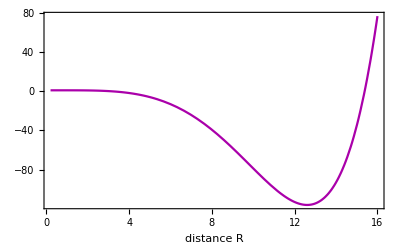

```mathematica
ftest2oo=Plot[q0oo/.{k->0},{x,0.2, 16},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Magenta]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->{False,False}]
```

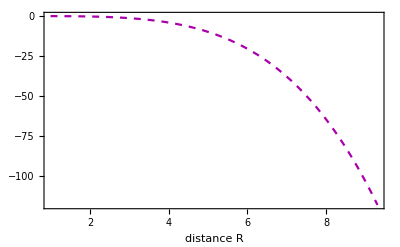

```mathematica
ftest22o=Plot[q2oo/.{k->0},{x,1, 9.3},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dashed,Darker[Magenta]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->{False,False}]
```

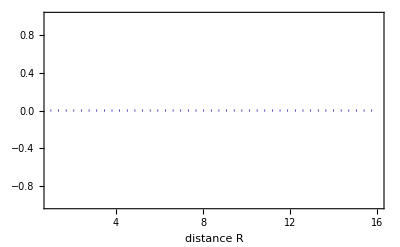

```mathematica
ftest4oo=Plot[q4oo/.{k->0},{x,1, 16},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dotted,Darker[Blue]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->{False,False}]
```

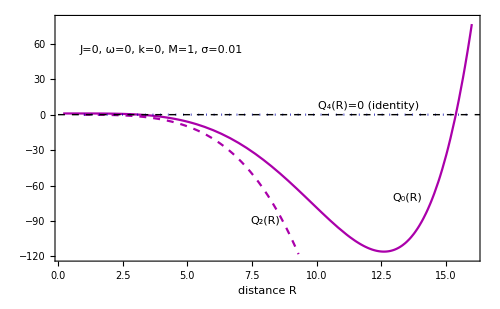

```mathematica
f3=Show[ftest2oo,ftest22o,ftest4oo,Graphics[{Inset[Framed["J=0, ω=0, k=0, M=1, σ=0.01"],{4,55},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{8,-90},BaseStyle->{Italic,Bold,Darker[Gray],FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)=0 (identity)",{12,7},BaseStyle->{Italic,Bold,Darker[Gray],FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{13.5,-70},BaseStyle->{Italic,Bold,Darker[Gray],FontFamily->"Times",12}]}], FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-120,80},Axes->{False,False}]
```

```mathematica
Export["D:f3.pdf",f3,"PDF"];
```

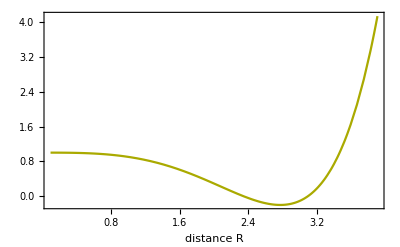

```mathematica
ftest2oon=Plot[q0oo/.{k->0.05},{x,0.1, 3.9},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Darker[Yellow]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->{False,False}]
```

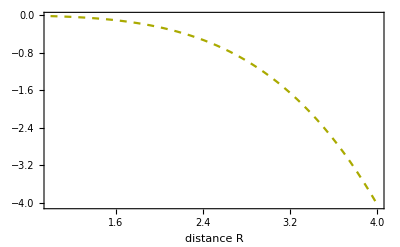

```mathematica
ftest22on=Plot[q2oo/.{k->0.05},{x,1, 4},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dashed,Darker[Yellow]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->{False,False}]
```

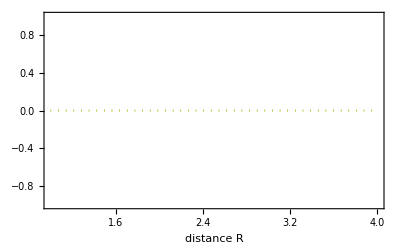

```mathematica
ftest4oon=Plot[q4oo/.{k->0.05},{x,1, 4},PlotRange->All,AxesOrigin->{3,0},Frame->True,FrameLabel->{"distance R",""},PlotStyle->{Dotted,Darker[Yellow]},AxesStyle->Black,LabelStyle->{FontFamily->"Arial",11,GrayLevel[0],Bold},Axes->{False,False}]
```

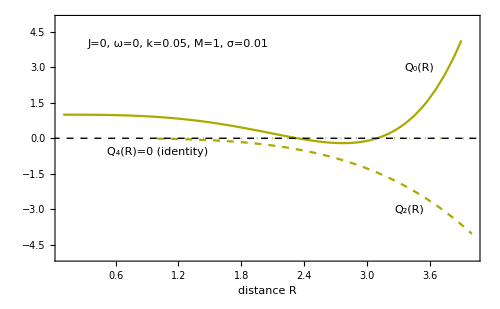

```mathematica
f4=Show[ftest2oon,ftest22on,ftest4oon,Graphics[{Inset[Framed["J=0, ω=0, k=0.05, M=1, σ=0.01"],{1.2,4},BaseStyle->{Italic,Bold,Black,FontFamily->"Times",12}]}],Graphics[{Inset["Q_2(R)",{3.4,-3},BaseStyle->{Italic,Bold,Darker[Gray],FontFamily->"Times",12}]}],Graphics[{Inset["Q_4(R)=0 (identity)",{1,-0.6},BaseStyle->{Italic,Bold,Darker[Gray],FontFamily->"Times",12}]}],Graphics[{Inset["Q_0(R)",{3.5,3},BaseStyle->{Italic,Bold,Darker[Gray],FontFamily->"Times",12}]}], FrameStyle->Directive[Black,Thick],Epilog->{{Dashed,Black,Line[{{0,0},{20,0}}]}},BaseStyle->{Large,Italic,Bold,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],ImageSize->500,PlotRange->{-5,5},Axes->{False,False}]
```